```mathematica
pdes={
RNA'[t]==Ktc RP P[t]-kdeg RNA[t]}
```

{RNA'[t]==Ktc RP P[t]-kdeg RNA[t]}

```mathematica
DSolve
```

DSolve

```mathematica
Integrate[t ⅇ^(-λ t),{t,0,∞}]
```

ConditionalExpression[1/λ^2,Re[λ]>0]

```mathematica
Integrate[ⅇ^(-λ t),t]
```

-ⅇ^(-t λ)/λ

```mathematica
Manipulate[LogLinearPlot[600*t ⅇ^(-λ t),{t,.001,10},PlotRange->{All,{0,Automatic}} ,Ticks->{{0.001,0.1,10},Automatic},AspectRatio->1.5],{λ,0.0001,10}]
```

```mathematica
PDF[ProbabilityDistribution[x ⅇ^-x,{x,0,∞}],x]
```

Piecewise[{{ⅇ^-x x, x>0}, {0, True}}]

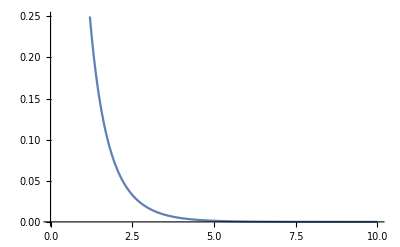

```mathematica
Plot[1/t ⅇ^-t,{t,0,10}]
```

```mathematica
ProbabilityDistribution[t ⅇ^(-10*t),{t,0,∞}]
```

ProbabilityDistribution[x ⅇ^(-10 x),{x,0,∞}]

```mathematica
PDF[ProbabilityDistribution[x ⅇ^(-10 x),{x,0,∞}],x]
```

Piecewise[{{ⅇ^(-10 x) x, x>0}, {0, True}}]

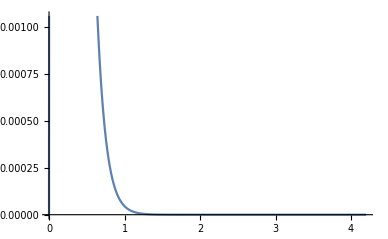

ⅇ^(-10 t) t

```mathematica
Plot[Piecewise[{{ⅇ^(-10x) x,x>0}},0],{x,0,4.2}]
```

```mathematica
ProbabilityDistribution[t ⅇ^(-t 10),{t,0.0001,100}]
```

ProbabilityDistribution[x ⅇ^(-10 x),{x,0.0001,100}]

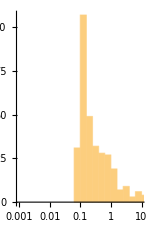

```mathematica
Histogram[1/RandomVariate[ProbabilityDistribution[t ⅇ^(-t /100),{t,0.001,1000}],500],{"Log",10},PlotRange->{{0.001,10},Automatic},Ticks->{{0.001,0.1,10},Automatic},AspectRatio->1.5,ImageSize->150]
```

```mathematica
Distribute
```

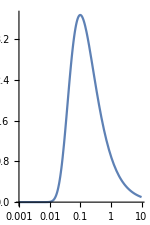

```mathematica
LogLinearPlot[t ⅇ^(-λ t)/.{λ->1/10,t-> 1/r},{r,0.001,10},Ticks->{{0.001,0.1,10},Automatic},AspectRatio->1.5,ImageSize->150,PlotRange->{All,{0,Automatic}} ]
```

```mathematica
solution=Assuming[ts>0&&λ>0&&5>a>1,Integrate[ⅇ^(-λ t)/(1+t^a/ts^a),{t,0,∞}]]
```

∫_0^∞ ⅇ^(-t λ)/(1+t^a ts^-a)ⅆt

```mathematica
(solution /.λ->1 )//FullSimplify
```

$Aborted

```mathematica
GraphicsColumn[Table[ContourPlot[solution ,{ts,0,15},{λ,0,2},PlotLegends->Placed[Automatic,Right],PlotRange->All,FrameLabel->{"Typical binding distance/translation speed","Translation initiation rate"},PlotLabel->"Fraction of dimerisation during translation",LabelStyle->{FontSize->Max[Scaled[.05],10]}],{a,1,5}]]
```

$Aborted

```mathematica
solution/.λ->12
```

ts CosIntegral[12 ts] Sin[12 ts]+1/2 ts Cos[12 ts] (π-2 SinIntegral[12 ts])

```mathematica
solution λ/.{λ->0.000001,ts->10}
```

0.0000157068

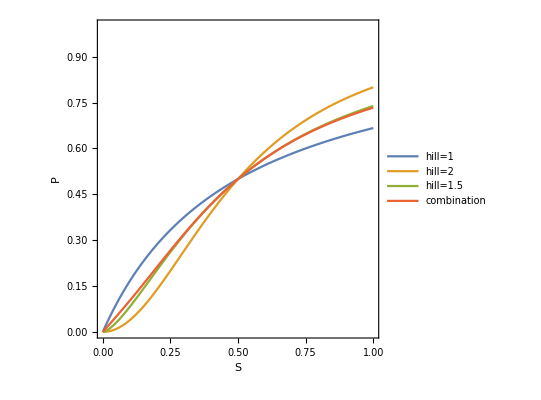

```mathematica
Plot[{1/(1+((1/2)/x)),1/(1+((1/2)/x)^2),1/(1+((1/2)/x)^1.5),(1/2)/(1+((1/2)/x))+(1/2)/(1+((1/2)/x)^2)},{x,0,1},AspectRatio->1,PlotRange->{0,1},Frame->True,FrameLabel->{"S","P"},PlotLegends->{"hill=1","hill=2","hill=1.5","combination"}]
```

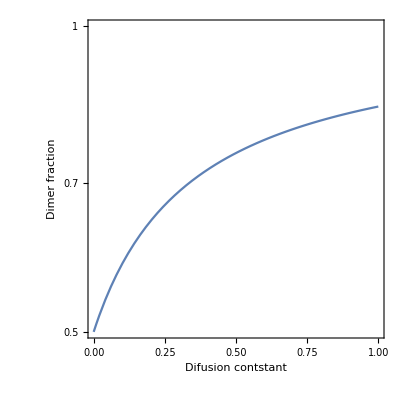

```mathematica
LogPlot[.5+(1/2)/(1+((1/2)/x)),{x,0,1},AspectRatio->1,PlotRange->{0,1},Frame->True,FrameLabel->{"Difusion contstant","Dimer fraction"}]
```

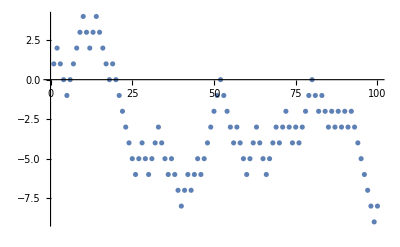

```mathematica
ListPlot[Accumulate[RandomChoice[{1,-1},100]]]
```

```mathematica
x^3
```

6 x

{{f[x,t]→(ⅇ^(-(-t v+x)^2/(4 t)))/(2 √π √t)}}

```mathematica
pdesol=DSolve[{D[f[x,t], t]==-v D[f[x,t], x]+D D[f[x,t], x,x],f[x,0]==DiracDelta[x]},f[x,t],{x,t}]⟦1,1,2⟧
```

(ⅇ^(-(-t v+x)^2/(4 D t)))/(2 √π √(D t))

```mathematica
{{f[x,t]->(ⅇ^(-(t v+x)^2/(4 t)))/(2 √π √t)}}⟦1,1,2⟧
```

(ⅇ^(-(t v+x)^2/(4 t)))/(2 √π √t)

```mathematica
Manipulate[DensityPlot[(ⅇ^(-(t v+x)^2/(4 t)))/(2 √π √t),{t,-4.5485638722888995,4.5485638722888995},{x,-8.600374137579358,8.600374137579358}],{v,-2,2}]
```

```mathematica
t-#&/@Accumulate[RandomVariate[ProbabilityDistribution[t ⅇ^(-t /10),{t,0.0001,100}],20]]
```

{-2.50207+t,-3.53253+t,-5.12066+t,-6.41471+t,-8.51961+t,-9.02104+t,-11.5657+t,-13.6731+t,-15.8897+t,-17.5478+t,-19.7816+t,-21.4977+t,-23.2172+t,-25.2527+t,-27.0126+t,-29.1218+t,-30.6848+t,-33.1765+t,-35.6949+t,-38.2468+t}

```mathematica
viersampls=(pdesol/.t->t-#)&/@Accumulate[RandomVariate[ProbabilityDistribution[t ⅇ^(-t /10),{t,0.0001,100}],4]]
```

{(ⅇ^(-(-(-2.3572+t) v+x)^2/(4 D (-2.3572+t))))/(2 √π √(D (-2.3572+t))),(ⅇ^(-(-(-3.55978+t) v+x)^2/(4 D (-3.55978+t))))/(2 √π √(D (-3.55978+t))),(ⅇ^(-(-(-4.68954+t) v+x)^2/(4 D (-4.68954+t))))/(2 √π √(D (-4.68954+t))),(ⅇ^(-(-(-6.86109+t) v+x)^2/(4 D (-6.86109+t))))/(2 √π √(D (-6.86109+t)))}

```mathematica
Manipulate[Quiet[DensityPlot[Total[{(ⅇ^(-(-(-2.357203966030376+t) v+x)^2/(4 D (-2.357203966030376+t))))/(2 √π √(D (-2.357203966030376+t))),(ⅇ^(-(-(-3.55978038982483+t) v+x)^2/(4 D (-3.55978038982483+t))))/(2 √π √(D (-3.55978038982483+t))),(ⅇ^(-(-(-4.689543752216828+t) v+x)^2/(4 D (-4.689543752216828+t))))/(2 √π √(D (-4.689543752216828+t))),(ⅇ^(-(-(-6.861086378460314+t) v+x)^2/(4 D (-6.861086378460314+t))))/(2 √π √(D (-6.861086378460314+t)))}],{t,8,10},{x,0,80},PlotRange->All,PlotPoints->100,ColorFunction->GrayLevel]],{v,1,20},{D,0.1,10}]
```

```mathematica
viersampls/.t->40/.v->1/.x->1
```

{2.04117×10^-6,3.81797×10^-6,6.91982×10^-6,0.0000123185}

```mathematica
{{f[x,t]->(ⅇ^((t v+x)^2/(4 t)))/(2 √π √-t)}}⟦1,1,2⟧
```

(ⅇ^((t v+x)^2/(4 t)))/(2 √π √-t)

```mathematica
points=Reap[Do[array[[RandomInteger[{1,360}]]]*=-1;Sow[Total[array]],10000]][[2,1]];
```

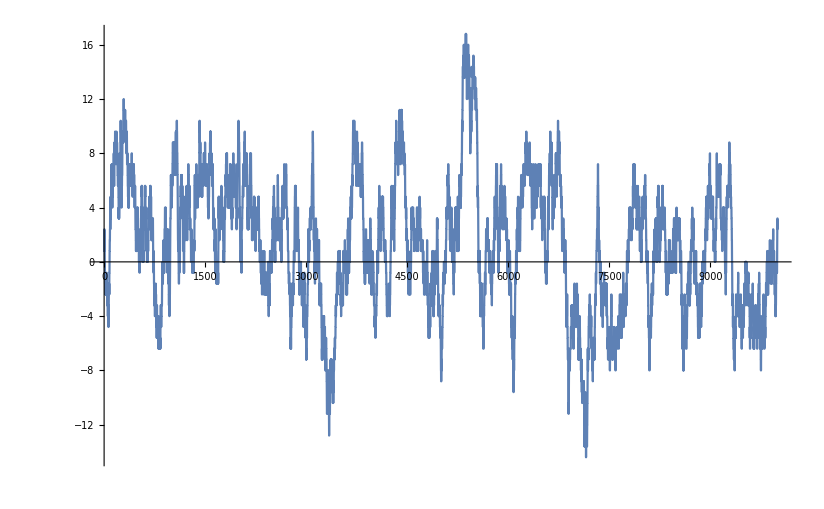

```mathematica
ListPlot[points,GridLines->{None, {90}},Joined->True]
```

```mathematica
array[[0]]
```

List

```mathematica
360*.4
```

144.

```mathematica
array=ConstantArray[.4,360];
```

```mathematica
;
```

```mathematica
%155[[2,1,;;-2]]
```

{1360,9997,Total[(-4)[4,-4,-4,-4,4,4,4,4,4,4,4,-4,4,-4,4,-4,-4,4,-4,4,-4,-4,4,4,-4,4,-4,-4,4,4,-4,-4,4,4,-4,4,4,4,4,4,-4,-4,-4,4,4,4,4,4,4,4,4,4,4,4,4,4,-4,-4,4,4,-4,-4,-4,-4,-4,4,4,4,4,-4,-4,-4,-4,-4,4,4,-4,4,4,4,-4,4,4,-4,4,-4,-4,4,4,-4,4,4,4,4,-4,4,-4,-4,-4,4,4,-4,-4,4,-4,4,4,-4,-4,-4,-4,4,4,-4,4,-4,4,-4,4,4,4,4,-4,-4,-4,-4,-4,4,4,-4,-4,-4,-4,-4,4,-4,-4,4,4,4,4,-4,-4,-4,-4,-4,-4,-4,4,-4,-4,4,4,-4,52,4,-4,-4,-4,4,-4,4,-4,4,-4,4,-4,4,-4,-4,4,4,-4,4,4,4,-4,4,4,-4,4,-4,4,-4,4,-4,-4,-4,-4,-4,4,4,-4,-4,4,4,-4,4,-4,-4,4,4,4,-4,4,-4,4,-4,4,-4,-4,-4,4,4,4,-4,-4,4,-4,4,4,4,4,-4,-4,4,4,-4,4,-4,4,-4,4,-4,-4,-4,4,-4,4,-4,4,4,4,-4,-4,-4,4,-4,-4,-4,-4,4,4,4,4,4,4,4,-4,-4,-4,4,-4,4,4,-4,-4,4,4,4,4,-4,-4,-4,-4,-4,4,4,-4,-4,-4,4,-4,4,4,-4,-4,-4,4,4,4,4,-4,4,-4,4,-4,-4,-4,4,4,4,4,-4,4,-4,-4,-4,-4]]}
 |  |  |  |

contour length amino acid is 4A,114332.  PubMed ID17028145

Length LacI 360 amino acids,https://www.uniprot.org/uniprot/J7QMK7

```mathematica
360
```

```mathematica
Orthogonalize
```

```mathematica
OrthogonalMatrixQ[{{{1,0,0},{-1,-1,1}},Orthogonalize[{{1,0,0},{-1,-1,1}}]}]
```

False

```mathematica
Orthogonalize[{{1,0,0},{-1,-1,1}}]
```

{{1,0,0},{0,-1/(√2),1/(√2)}}

```mathematica
Transpose[{{1,0,0},{0,-1/(√2),1/(√2)}}]
```

{{1,0},{0,-1/(√2)},{0,1/(√2)}}

```mathematica
200
```

(8 π)/3-(π (2-√(x^2))^2 (x^2+4 √(x^2)))/(12 √(x^2))

```mathematica
RegionIntersection[Ball[{0,0,0},r],Ball[{0,0,x},r]]
```

BooleanRegion[#1&&#2&,{Ball[{0,0,0},r],Ball[{0,0,x},r]}]

```mathematica
Simplify[(8 π)/3-(π (2-√(x^2))^2 (x^2+4 √(x^2)))/(12 √(x^2))]
```

-1/12 π (-4+√(x^2)) (2+√(x^2))^2

```mathematica
RegionIntersection[Ball[{0,0,0},1],Ball[{0,0,x},1]]
```

BooleanRegion[#1&&#2&,{Ball[{0,0,0},1],Ball[{0,0,x},1]}]

(π (2 r-√(x^2))^2 (x^2+4 r √(x^2)))/(12 √(x^2))

```mathematica
RegionMeasure
```

```mathematica
efC=Assuming[x>0,FullSimplify[(RegionIntersection[Ball[{0,0,0},r],Ball[{0,0,x},r]]//RegionMeasure)/(4/3 π r^3)]]
```

$Aborted

```mathematica
efCinit=Piecewise[{{Volume[RegionIntersection[Ball[{0,0,0},r+dr],Ball[{0,0,Δx},r]]],2r+dr>Δx}},0]
```

\text{efCinit}=
\begin{array}{cc}
 \{ & 
\begin{array}{cc}
 \text{Volume}[\text{RegionIntersection}[\text{Ball}[\{0,0,0\},r+\text{dr}],\text{Ball}[\{0,0,\text{$\Delta $x}\},r]]] & 2 r+\text{dr}>\text{$\Delta $x} \\
 0 & \text{True} \\
\end{array}
 \\
\end{array}

```mathematica
efCinit=Piecewise[{{Volume[RegionIntersection[Ball[{0,0,0},r],Ball[{0,0,x},r]]],2r>x}},0]
```

Piecewise[{{(π (2 r-√(x^2))^2 (x^2+4 r √(x^2)))/(12 √(x^2)), 2 r>x}, {0, True}}]

```mathematica
Manipulate[Evaluate[efCinit],{x,-8,8},{r,-8,8}]
```

```mathematica
(π (2 r-√(x^2))^2 (x^2+4 r √(x^2)))/(12 √(x^2))
```

```mathematica
efCinit=Integrate[Boole[x^2+y^2+z^2<R^2&&(x-d)^2+y^2+z^2<R^2],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->R>0&&d>0]/(4/3π R^3)
```

(3 (Piecewise[{{1/12 π (d-2 R)^2 (d+4 R), d>0&&d-2 R<0}, {0, True}}]))/(4 π R^3)

```mathematica
π
```

```mathematica
Manipulate[Plot[(3 (Piecewise[{{(4 π R^3)/3, d==0&&R>0}, {-1/12 π (d-4 R) (d+2 R)^2, d<0&&d+2 R>0}, {1/12 π (d-2 R)^2 (d+4 R), d>0&&d-2 R<0}, {0, True}}]))/(4 π R^3),{d,0,2}],{R,0.1,1}]
```

```mathematica
Assuming[d>0,FullSimplify[efCinit]]
```

Piecewise[{{((d-2 R)^2 (d+4 R))/(16 R^3), d<2 R}, {0, True}}]

```mathematica
Integrate[((d-2 R)^2 (d+4 R))/(16 R^3),{R,d/2,r2}]
```

$Aborted

```mathematica
efCinitass=Assuming[d<2 R&&d>0,FullSimplify[efCinit]]
```

((d-2 R)^2 (d+4 R))/(16 R^3)

```mathematica
Integrate[1,{x,2,-4}]
```

-6

```mathematica
test=Assuming[d>0&&r2>0,Integrate[ⅇ^(-λ d)efCinitass^2/(μ+efCinitass^2)/.μ->1,{R,0(*d/2*),r2},{d,0,2r2}]/r2]
```

$Aborted

```mathematica
efCinit
```

((d-2 R)^2 (d+4 R))/(16 R^3)

```mathematica
NIntegrate[ⅇ^(-λ d)efCinit^2/(μ+efCinit^2)/.μ->1/.λ->.1,{R,0,400},{d,0,∞}]/400
```

4.54928

```mathematica
Plot3D[NIntegrate[ⅇ^(-λ d)efCinit^2/(μ+efCinit^2)/.μ->1,{R,0,r2},{d,0,∞}]/r2,{λ,0,10},{r2,0,400}]
```

-Graphics3D-

```mathematica
LogPlot
```

```mathematica
Integrate[ⅇ^(-λ d),{d,0,∞}]
```

ConditionalExpression[1/λ,Re[λ]>0]

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/ruud/Dropbox/Documents/PhD/dimerisation/model

```mathematica
hexToRGB[hex_]:=RGBColor@@(N[FromDigits[StringJoin[#],16]/255]&/@Partition[Characters[hex],2]);
hexToRGB[hex_]:=RGBColor["#"<>hex];Themes`AddThemeRules["Export",DefaultPlotStyle->Thread@Directive[hexToRGB/@{"CCBB44","AA3377","66CCEE","EE6677","4477AA","228833","EE6677","BBBBBB"},Thick],Background->None,LabelStyle->{FontSize->10,FontFamily->"CMU Serif"},ImageSize->200,PlotMarkers->{Automatic,Small}];
```

```mathematica
Export["alpha_calc_dimer.pdf",Row[Append[Table[DensityPlot[1NIntegrate[ⅇ^(-λ d)efCinit^2/(μ+efCinit^2),{R,0,r2},{d,0,∞}]/r2*λ,{λ,0.001,10},{r2,0,400},FrameLabel->{{"Initiation Rate(1/s)",None},{"Potein length(AA)","Reaction parameter:"<>ToString[μ]}},ScalingFunctions->{"Log",None},(*PlotRange->{Automatic,Automatic,{0,1}}*)ColorFunctionScaling->False,ImageSize->200,LabelStyle->{FontSize->10,FontFamily->"cmr10"},ImagePadding->{{40,20},{30,20}},PlotRangePadding->None],{μ,{0.1,1}}],BarLegend["M10DefaultDensityGradient",LabelStyle->{FontSize->10,FontFamily->"cmr10",Black},LegendLabel->Placed["Fraction Translation\n mediated dimerisation",Right,Rotate[#,90Degree]&],LegendMarkerSize->160,LegendMargins->0]]]];SystemOpen["alpha_calc_dimer.pdf"]
```

### What if we change to area integration

```mathematica
efCinit=Integrate[Boole[x^2+y^2+z^2<R^2&&(x-d)^2+y^2+z^2<R^2],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->R>0&&d>0]/(4/3π R^3)
```

(3 (Piecewise[{{1/12 π (d-2 R)^2 (d+4 R), d>0&&d-2 R<0}, {0, True}}]))/(4 π R^3)

```mathematica
Series[f[x]/(1+f[x])]
```

Series::argmu: Series called with 1 argument; 2 or more arguments are expected.

Series[f[x]/(1+f[x])]

```mathematica
f[d2_?NumericQ,r_]:=f[d2,r]=((*Print[d2];*)NIntegrate[efCinit^2/.{d->d2},{R,0,r}])
```

```mathematica
N[f[1,400]]
```

390.622

```mathematica
Export["alpha_calc_dimer_new_and_improved.pdf",Row[Append[Table[DensityPlot[1NIntegrate[ⅇ^(-λ d)f[d,r2]/(μ r2+f[d,r2]),{d,0,∞}]*λ,{λ,0.001,10},{r2,0,400},FrameLabel->{{"Potein length(AA)",None},{"Initiation Rate(1/s)","Reaction parameter:"<>ToString[1/μ]}},ScalingFunctions->{"Log",None},(*PlotRange->{Automatic,Automatic,{0,1}}*)ColorFunctionScaling->False,ImageSize->200,LabelStyle->{FontSize->10,FontFamily->"cmr10"},ImagePadding->{{40,20},{30,20}},PlotRangePadding->None],{μ,{1,1/10}}],BarLegend["M10DefaultDensityGradient",LabelStyle->{FontSize->10,FontFamily->"cmr10",Black},LegendLabel->Placed["Fraction Translation\n mediated dimerisation",Right,Rotate[#,90Degree]&],LegendMarkerSize->160,LegendMargins->0]]]];SystemOpen["alpha_calc_dimer_new_and_improved.pdf"]
```

```mathematica
Boxed
```

```mathematica
}
```

```mathematica
SystemOpen["alpha_calc_dimer.pdf"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["alpha_calc_dimer.pdf"]]]
```

```mathematica
Blend[Color
```

```mathematica
BarLegend[Blend[{RGBColor["#e9f2fa"],RGBColor["#084387"]},#1]&]
```

BarLegend[Blend[{RGBColor[#e9f2fa],RGBColor[#084387]},#1]&]

```mathematica
classicDensityPlot
```

Blend[{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.563820859082933, 0.527565423056382, 0.909498741130694],RGBColor[0.762631, 0.846998, 0.914031],RGBColor[0.941176, 0.906538, 0.834043]},#1]&

```mathematica
Blend["M10DefaultDensityGradient",#1]&@0.1
```

RGBColor[0.274, 0.4, 0.658]

```mathematica
M10DefaultDensityGradient
```

M10DefaultDensityGradient

```mathematica
Trace[DensityPlot[x y,{x,y}∈Disk[]],_Blend&]
```

{{{{{{{{{{{{{{Blend[M10DefaultDensityGradient,#1]&},Blend[M10DefaultDensityGradient,#1]&},{{{{{{{{{{{{{Blend[M10DefaultDensityGradient,#1]&}}},{{{Blend[M10DefaultDensityGradient,#1]&}}}}}}}}}}}}}}}}}}}}}}}}}

```mathematica
BarLegend["CMYKColors"]
```

```mathematica
ColorFunction
```

ColorFunction

```mathematica
Plot3D[Assuming[d>0&&r2>0,Integrate[ⅇ^(-λ d)efCinitass^2/(μ+efCinitass^2)/.μ->1,{R,d/2,r2},{d,0,2r2}]/r2],{λ,0,10},{r2,0,400},PlotLegends->Automatic,AxesLabel->{"Transcribed Protein length[AA]","Inter-ribosome distande[AA]"}(*,ColorFunction->"Monochrome"*),Exclusions->None,ExclusionsStyle->Red,PlotPoints->30]
```

$Aborted

```mathematica
Integrate[efCinit,R]/.R->0//FullSimplify
```

0

```mathematica
efC=Integrate[efCinit,{R,0,r}]
```

∫_0^r (3 (Piecewise[{{(4 π R^3)/3, d==0&&R>0}, {-1/12 π (d-4 R) (d+2 R)^2, d<0&&d+2 R>0}, {1/12 π (d-2 R)^2 (d+4 R), d>0&&d-2 R<0}, {0, True}}]))/(4 π R^3)ⅆR

```mathematica
tes2=test/r2//FullSimplify
```

Piecewise[{{1/(96 r2)(-24 d+48 r2+d RootSum[d^6-24 d^4 #1^2+32 d^3 #1^3+144 d^2 #1^4-384 d #1^5+512 #1^6&,(d^5 Log[1/2 (d-2 #1)]-24 d^3 Log[1/2 (d-2 #1)] #1^2+32 d^2 Log[1/2 (d-2 #1)] #1^3+144 d Log[1/2 (d-2 #1)] #1^4-384 Log[1/2 (d-2 #1)] #1^5)/(d^4 #1-2 d^3 #1^2-12 d^2 #1^3+40 d #1^4-64 #1^5)&]-d RootSum[d^6-24 d^4 #1^2+32 d^3 #1^3+144 d^2 #1^4-384 d #1^5+512 #1^6&,(d^5 Log[r2-#1]-24 d^3 Log[r2-#1] #1^2+32 d^2 Log[r2-#1] #1^3+144 d Log[r2-#1] #1^4-384 Log[r2-#1] #1^5)/(d^4 #1-2 d^3 #1^2-12 d^2 #1^3+40 d #1^4-64 #1^5)&]), d<2 r2}, {0, True}}]

```mathematica
Plot3D[tes2,{r2,0,360},{d,0,200},PlotLegends->Automatic,AxesLabel->{"Transcribed Protein length[AA]","Inter-ribosome distande[AA]"}(*,ColorFunction->"Monochrome"*),Exclusions->None,ExclusionsStyle->Red,PlotPoints->30]
```

-Graphics3D-

```mathematica
Manipulate[DensityPlot[efC^2/(1/μ+efC^2),{d,0,2},{r,0,1},Frame->True,FrameLabel->{"Ribosome distance/finnished length","Translation dimerisation fraction"},PlotLabel->"fully formed proteins difusse with ribosomes",PlotRange->{0,1}],{{μ,.5,"dimerisation variable"},.1,100} ]
```

```mathematica
solution=Assuming[ts>0&&λ>0&&5>a>1,Integrate[ⅇ^(-λ t)/(1+t^a/ts^a),{t,0,∞}]]
```

```mathematica
test3=Integrate[Assuming[d<2r2,Simplify[ⅇ^(-λ d)tes2]],{d,0,2r2}]
```

```mathematica
test3=Integrate[Assuming[d<2r2,Simplify[ⅇ^(-λ d)test]],{d,0,2r2}]
```

$Aborted

```mathematica
Assuming[r2>0,Integrate[ⅇ^(-λ d)tes2,{d,0,2r2}]]
```

$Aborted

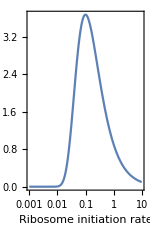

```mathematica
LogLinearPlot[t ⅇ^(-λ t)/.{λ->1/10,t-> 1/r},{r,0.001,10},Ticks->{{0.001,0.1,10},Automatic},AspectRatio->1.5,ImageSize->150,PlotRange->{All,{0,Automatic}} ,Frame->True,FrameLabel->{"Ribosome initiation rate","Probability"}]
```

```mathematica
efC=1/12 π (-2+x)^2 (4+x)
```

1/12 π (-2+x)^2 (4+x)

```mathematica
E
```

```mathematica
1/12 π (-2+x)^2 (4+x)
```

(8 π)/3

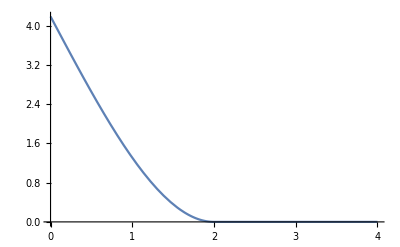

Ball[{0,0,1}]

```mathematica
Plot[RegionIntersection[Ball[{0,0,0}],Ball[{0,0,x}]]//RegionMeasure,{x,0,4}]
```